# economic analysis

## import data

(1) raw data 
(2) median
(3) uncertainty
(4) full
(5) cbp consumption

### preparing directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCeaalls"]]}];
```

### load data

```mathematica
nod=4; (*# of indications*)

(*MODEL OUTPUTS*)
Quiet[dataP=ToExpression[Import["pneumonia output.xlsx","Data"]]; (*pneumonia*)
dataS=ToExpression[Import["bacteremia output.xlsx","Data"]]; (*bacteremia*)
dataU=ToExpression[Import["uti output.xlsx","Data"]]; (*uti*)
dataA=ToExpression[Import["cIAI output.xlsx","Data"]];] (*uti*)
```

```mathematica
(*DATA & PARAMETERS*)
mdataP=Import["AMR_Datasheet.xlsx",{"Data","Pneu_model"}]; (*PNEUMONIA*)
mdataP = mdataP[[All,2;;]]; 
years = mdataP[[1]]; (*years of available data*)
tt = Length[years];  (*# years of available data*)
pathogens=mdataP[[15]][[1;;3]]; (*pathogen headers*)
nop = Length[pathogens]; (*# of pathogens*)
cbpP=mdataP[[16]][[-1]]; (*proportion of pneumonia patients prescribed cbps*)
inappP=mdataP[[17]][[1]]; (*inappropriate cbp prescription*)
pathP=Table[mdataP[[i]][[-1]],{i,18,20}]; 
(*proportion of pneumonia for PA, AB, KP*)

edataP=mdataP[[21;;]];(*data for economic and health outcomes*) 
stw = edataP[[1]][[1]]; (*reduction in inappropriate therapy*)
pP=edataP[[13]];  (*prevalence of pneumonia*)

mdataS=Import["AMR_Datasheet.xlsx",{"Data","Bacteremia_model"}]; (*BACTEREMIA*)
mdataS = mdataS[[All,2;;]]; 
cbpS=mdataS[[16]][[-1]]; (*proportion of patients prescribed cbps*)
inappS=mdataS[[17]][[1]]; (*inappropriate cbp prescription*)
pathS=Table[mdataS[[i]][[-1]],{i,18,20}]; 
(*proportion of for PA, AB, KP*)

edataS=mdataS[[21;;]];(*data for economic and health outcomes*)
pS=edataS[[13]]; (*prevalence of bacteremia*)

mdataU=Import["AMR_Datasheet.xlsx",{"Data","UTI_model"}]; (*UTI*)
mdataU = mdataU[[All,2;;]]; 
cbpU=mdataU[[16]][[-1]]; (*proportion of patients prescribed cbps*)
inappU=mdataU[[17]][[1]]; (*inappropriate cbp prescription*)
pathU=Table[mdataU[[i]][[-1]],{i,18,20}]; 
(*proportion of for PA, AB, KP*)

edataU=mdataU[[21;;]];(*data for economic and health outcomes*)
pU=edataU[[13]]; (*prevalence of UTI*)

mdataA=Import["AMR_Datasheet.xlsx",{"Data","cIAI_model"}]; (*UTI*)
mdataA = mdataA[[All,2;;]]; 
cbpA=mdataA[[16]][[-1]]; (*proportion of patients prescribed cbps*)
inappA=mdataA[[17]][[1]]; (*inappropriate cbp prescription*)
pathA=Table[mdataA[[i]][[-1]],{i,18,20}]; 
(*proportion of for PA, AB, KP*)

edataA=mdataA[[21;;]];(*data for economic and health outcomes*)
pA=edataA[[13]][[7;;]]; (*prevalence of UTI*)

p={pP,pS,pU,pA}; (*prevalence*)

yvals=Range[2000,2040];
```

## model fit plots & projections

### plot consumption

```mathematica
cbpdatP=Table[Transpose@{Range[2000,2040],dataP[[5]][[k]][[i]][[2;;]]},{k,1,4},{i,2,3}];
cbpdatS=Table[Transpose@{Range[2000,2040],dataS[[5]][[k]][[i]][[2;;]]},{k,1,4},{i,2,3}];
cbpdatU=Table[Transpose@{Range[2000,2040],dataU[[5]][[k]][[i]][[2;;]]},{k,1,4},{i,2,3}];
cbpdatA=Table[Transpose@{Range[2000,2040],dataA[[5]][[k]][[i]][[2;;]]},{k,1,4},{i,2,3}];
```

```mathematica
(*plot font sizes, colors, etc.*)
color={GrayLevel[0.5],RGBColor[0,0.45,0.70],RGBColor[0.9,0.6,0],RGBColor[0,0.6,0.5]}; (*green=AB, blue=KB*)
marker=None;
label={"Pneumonia","Bacteremia"};
thick=0.02;
markers=0.05;
(*font sizes*)
labelf=28; 
axesf=20;
axeslf=24;
legendf=20;
```

```mathematica
nop=2;

(*a,b,c,d are temporary variables*)
i=1; (*pneu, AB*)
a=Show[ListLinePlot[{cbpdatP[[1]][[i]][[15;;]],cbpdatP[[2]][[i]],cbpdatP[[3]][[i]],cbpdatP[[4]][[i]]},PlotStyle-> {{color[[1]],Thickness[thick]},{color[[2]],Thickness[thick],Dashed},{color[[3]],Thickness[thick],DotDashed},{color[[4]],Thickness[thick],Dotted}},PlotLabel->Style[label[[1]],Black,labelf,FontFamily-> "Helvetica"],PlotRange->{{2000,2040},{0,2}},
Frame-> {True,True,False,False},FrameTicks->{{{0.5,{1,"1.0"},1.5,{2,"2.0"}},None},{None,None}},FrameStyle-> Directive[Black,Thick,axesf,FontFamily-> "Helvetica"]],
ListLinePlot[cbpdatP[[1]][[i]][[1;;15]],PlotStyle-> {color[[1]]},PlotMarkers-> {marker,markers}]];

i=2; (*pneu, KP*)
b=Show[ListLinePlot[{cbpdatP[[1]][[i]][[15;;]],cbpdatP[[2]][[i]],cbpdatP[[3]][[i]],cbpdatP[[4]][[i]]},PlotStyle-> {{color[[1]],Thickness[thick]},{color[[2]],Thickness[thick],Dashed},{color[[3]],Thickness[thick],DotDashed},{color[[4]],Thickness[thick],Dotted}},
PlotRange->{{2000,2040},{0,2}},
Frame-> {True,True,False,False},FrameTicks->{{{0.5,{1,"1.0"},1.5,{2,"2.0"}},None},{{2000,2020,2040},None}},FrameStyle-> Directive[Black,Thick,axesf,FontFamily-> "Helvetica"]],
ListLinePlot[cbpdatP[[1]][[i]][[1;;15]],PlotStyle-> {color[[1]]},PlotMarkers-> {marker,markers}]];

i=1; (*bacteremia, AB*)
c=Show[ListLinePlot[{cbpdatS[[1]][[i]][[15;;]],cbpdatS[[2]][[i]],cbpdatS[[3]][[i]],cbpdatS[[4]][[i]]},PlotStyle-> {{color[[1]],Thickness[thick]},{color[[2]],Thickness[thick],Dashed},{color[[3]],Thickness[thick],DotDashed},{color[[4]],Thickness[thick],Dotted}},PlotLabel->Style[label[[2]],Black,labelf,FontFamily-> "Helvetica"],
PlotRange->{{2000,2040},{0,0.2}},
Frame-> {True,True,False,False},FrameTicks->{{{0.05,{0.10,"0.10"},0.15,{0.20,"0.20"}},None},{None,None}},FrameStyle-> Directive[Black,Thick,axesf,FontFamily-> "Helvetica"]],
ListLinePlot[cbpdatS[[1]][[i]][[1;;15]],PlotStyle-> {color[[1]]},PlotMarkers-> {marker,markers}]];

i=2; (*bacteremia, KP*)
d=Show[ListLinePlot[{cbpdatS[[1]][[i]][[15;;]],cbpdatS[[2]][[i]],cbpdatS[[3]][[i]],cbpdatS[[4]][[i]]},PlotStyle-> {{color[[1]],Thickness[thick]},{color[[2]],Thickness[thick],Dashed},{color[[3]],Thickness[thick],DotDashed},{color[[4]],Thickness[thick],Dotted}},PlotRange->{{2000,2040},{0,0.2}},
Frame-> {True,True,False,False},FrameTicks->{{{0.05,{0.10,"0.10"},0.15,{0.20,"0.20"}},None},{{2000,2020,2040},None}},FrameStyle-> Directive[Black,Thick,axesf,FontFamily-> "Helvetica"]],
ListLinePlot[cbpdatS[[1]][[i]][[1;;15]],PlotStyle-> {color[[1]]},PlotMarkers-> {marker,markers}]];

e={Labeled[GraphicsRow[{a,c},ImageSize-> 700,AspectRatio->Automatic,Spacings-> 0],"A. baumannii", Left,RotateLabel-> True,LabelStyle-> Directive[Italic, labelf,FontFamily-> "Helvetica"]],
Labeled[GraphicsRow[{b,d},ImageSize-> 700,AspectRatio->Automatic,ImageMargins->{{10,0},{0,0}},Spacings-> 0],"K. pneumoniae", Left,RotateLabel-> True,LabelStyle-> Directive[Italic, labelf,FontFamily-> "Helvectica"]]};


lg=LineLegend[{color[[1]],{color[[2]],Thickness[thick],Dashed},{color[[3]],Thickness[thick],DotDashed},{color[[4]],Thickness[thick],Dotted}},{"Status quo","2020 stewardship","2025 stewardship","2030 stewardship"},LabelStyle-> Directive[legendf,Italic,FontFamily-> "Helvetica"],LegendLayout->{"Row",1},LegendMargins-> 30];

cbpplot=Legended[Labeled[GraphicsColumn[e,ImageSize-> 800,Alignment-> Left,AspectRatio->0.6,Frame-> All, FrameStyle-> White],{"CBP prescription (SUs/1000 ppl)","Years"}, {Left,Bottom},RotateLabel-> True,LabelStyle-> Directive[ axeslf,Bold,FontFamily-> "Helvetica"]],Placed[lg,Below]];

(*Export["cbp.jpeg",cbpplot];*)
```

### plot raw data & uncertainty

```mathematica
ss=1000;
nop=3;

rdatP=Table[RandomVariate[
BetaDistribution[dataP[[1]][[2]][[i]][[s]][[t]],(dataP[[1]][[1]][[i]][[s]][[t]]-dataP[[1]][[2]][[i]][[s]][[t]])],1][[1]]
,{i,1,nop},{s,1,ss},{t,1,tt}];
rdatB=Table[RandomVariate[
BetaDistribution[dataS[[1]][[2]][[i]][[s]][[t]],(dataS[[1]][[1]][[i]][[s]][[t]]-dataS[[1]][[2]][[i]][[s]][[t]])],1][[1]]
,{i,1,nop},{s,1,ss},{t,1,tt}];
rdatU=Table[RandomVariate[
BetaDistribution[dataU[[1]][[2]][[i]][[s]][[t]],(dataU[[1]][[1]][[i]][[s]][[t]]-dataU[[1]][[2]][[i]][[s]][[t]])],1][[1]]
,{i,1,nop},{s,1,ss},{t,1,tt}];
rdatA=Table[RandomVariate[
BetaDistribution[dataA[[1]][[2]][[i]][[s]][[t]],(dataA[[1]][[1]][[i]][[s]][[t]]-dataA[[1]][[2]][[i]][[s]][[t]])],1][[1]]
,{i,1,nop},{s,1,ss},{t,1,tt}];
```

```mathematica
(*95%*)
p95=Table[
Transpose[rdatP[[i]]][[t]][[Ordering[Transpose[rdatP[[i]]][[t]]]]][[26;;975]],
{i,1,nop},{t,1,tt}]; (*pneumonia*)
pm =Table[Median[Transpose[p95[[i]]]],{i,1,nop}];
pyer1=Table[Median[Transpose[p95[[i]]]]-Transpose[p95[[i]]][[1]],{i,1,nop}];
pyer2=Table[Transpose[p95[[i]]][[-1]]-Median[Transpose[p95[[i]]]],{i,1,nop}];

b95=Table[
Transpose[rdatB[[i]]][[t]][[Ordering[Transpose[rdatB[[i]]][[t]]]]][[26;;975]],
{i,1,nop},{t,1,tt}]; (*bacteremia*)
bm =Table[Median[Transpose[b95[[i]]]],{i,1,nop}];
byer1=Table[Median[Transpose[b95[[i]]]]-Transpose[b95[[i]]][[1]],{i,1,nop}];
byer2=Table[Transpose[b95[[i]]][[-1]]-Median[Transpose[b95[[i]]]],{i,1,nop}];

u95=Table[
Transpose[rdatU[[i]]][[t]][[Ordering[Transpose[rdatU[[i]]][[t]]]]][[26;;975]],
{i,1,nop},{t,1,tt}]; (*UTI*)
um =Table[Median[Transpose[u95[[i]]]],{i,1,nop}];
uyer1=Table[Median[Transpose[u95[[i]]]]-Transpose[u95[[i]]][[1]],{i,1,nop}];
uyer2=Table[Transpose[u95[[i]]][[-1]]-Median[Transpose[u95[[i]]]],{i,1,nop}];

a95=Table[
Transpose[rdatA[[i]]][[t]][[Ordering[Transpose[rdatA[[i]]][[t]]]]][[26;;975]],
{i,1,nop},{t,1,tt}]; (*cIAI*)
am =Table[Median[Transpose[a95[[i]]]],{i,1,nop}];
ayer1=Table[Median[Transpose[a95[[i]]]]-Transpose[a95[[i]]][[1]],{i,1,nop}];
ayer2=Table[Transpose[a95[[i]]][[-1]]-Median[Transpose[a95[[i]]]],{i,1,nop}];
```

```mathematica
errorPlot[plot_,data_,xer_,yer_,label_]:=With[{tr=Transpose@data,arrow=Graphics[{Gray,Thin,Line[{{0,1/2},{0,-1/2}}]}]},Module[{PlusMinus,limits,limitsRescaled,dataRescaled,lines,scale},scale=plot/.{ListPlot->{#&,#&},ListLogPlot->{#&,Log},ListLogLogPlot->{Log,Log},ListLogLinearPlot->{Log,#&}};
PlusMinus[a_,b_]:={a-b[[1]],a+b[[2]]};
limits=MapThread[MapThread[PlusMinus,{#,#2}]&,{tr,{xer,yer}}];
limitsRescaled=MapThread[Compose,{scale,limits}];
dataRescaled=MapThread[Compose,{scale,tr}];
lines=Flatten[MapAt[Reverse,MapThread[{{#2[[1]],#},{#2[[2]],#}}&,{Reverse@dataRescaled,limitsRescaled},2],{2,;;,;;}],1];
Show[plot[data,PlotStyle->{Black,AbsolutePointSize@5},Axes->True,Frame->None],Graphics[{Arrowheads[{{-.02,0,arrow},{.02,1,arrow}}],Gray,Arrow[lines]}],PlotRange->({Min[#],Max[#]}&/@Transpose@Flatten[lines,1])]]]
```

```mathematica
plotDp=ConstantArray[Null,nop]; (*data*)
For[k=1,k≤ nop,k++,
plotDp[[k]]=
errorPlot[ListPlot,Transpose@{years,pm[[k]]},ConstantArray[{0,0},15],Transpose@{pyer1[[k]],
pyer2[[k]]},pathogens[[k]]]](*data, xer, yer*)

plotDs=ConstantArray[Null,nop]; (*data*)
For[k=1,k≤ nop,k++,
plotDs[[k]]=
errorPlot[#,Transpose@{years,bm[[k]]},ConstantArray[{0,0},15],Transpose@{byer1[[k]],
byer2[[k]]},pathogens[[k]]]&/@{ListPlot}](*data, xer, yer*)

plotDu=ConstantArray[Null,nop]; (*data*)
For[k=1,k≤ nop,k++,
plotDu[[k]]=
errorPlot[#,Transpose@{years,um[[k]]},ConstantArray[{0,0},15],Transpose@{uyer1[[k]],
uyer2[[k]]},pathogens[[k]]]&/@{ListPlot}](*data, xer, yer*)

plotDa=ConstantArray[Null,nop]; (*data*)
For[k=1,k≤ nop,k++,
plotDa[[k]]=
errorPlot[#,Transpose@{years,am[[k]]},ConstantArray[{0,0},15],Transpose@{ayer1[[k]],
ayer2[[k]]},pathogens[[k]]]&/@{ListPlot}](*data, xer, yer*)


plotData={plotDp,plotDs,plotDu,plotDa};
```

```mathematica
(*(*test significance of correlation between consumption + resistance*)
a=Table[
SpearmanRankTest[dataP[[5]][[1]][[i]][[2;;16]],pm[[i]]],{i,1,nop}];
b=Table[
SpearmanRankTest[dataS[[5]][[1]][[i]][[2;;16]],bm[[i]]],{i,1,nop}];
c=Table[
SpearmanRankTest[dataU[[5]][[1]][[i]][[2;;16]],um[[i]]],{i,1,nop}];
d=Table[
SpearmanRankTest[dataA[[5]][[1]][[i]][[2;;16]],am[[i]]],{i,1,nop}];

params= Join[{a},{b},{c},{d}];
headings1=Prepend[params,pathogens];
headings2=MapThread[Prepend,{headings1,{"p","Pneumonia","Bacteremia","UTI","cIAI"}}];
Grid[headings2,Frame-> All]
*)
```

### unformatted plots

#### uncertainty

```mathematica
nop=3;

plota=ConstantArray[Null,nop]; (*model + status quo*)
plotb=ConstantArray[Null,nop]; (*intervention- stewardship*)
plotc=ConstantArray[Null,nop];
plotd=ConstantArray[Null,nop];

For[k=1, k≤nop,k++,

plota[[k]] ={ListLinePlot[Table[Transpose@{yvals,dataP[[3]][[1]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],PlotRange-> All,AxesOrigin-> {years[[1]],0}],ListLinePlot[Table[Transpose@{yvals,dataS[[3]][[1]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals,dataU[[3]][[1]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],PlotRange->All,Filling->{1->{2}}, FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals,dataA[[3]][[1]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],PlotRange->All,Filling->{1->{2}}, FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}]
};


plotb[[k]]={ListLinePlot[Table[Transpose@{yvals[[15;;]],dataP[[3]][[2]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],ListLinePlot[Table[Transpose@{yvals[[15;;]],dataS[[3]][[2]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataU[[3]][[2]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotRange->All,Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataA[[3]][[2]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotRange->All,Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}]};

plotc[[k]]={ListLinePlot[Table[Transpose@{yvals[[15;;]],dataP[[3]][[3]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],ListLinePlot[Table[Transpose@{yvals[[15;;]],dataS[[3]][[3]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataU[[3]][[3]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotRange->All,Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataA[[3]][[3]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotRange->All,Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}]};

plotd[[k]]={ListLinePlot[Table[Transpose@{yvals[[15;;]],dataP[[3]][[4]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],ListLinePlot[Table[Transpose@{yvals[[15;;]],dataS[[3]][[4]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataU[[3]][[4]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotRange->All,Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataA[[3]][[4]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotRange->All,Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}]};

]
(*{4 (pneumonia, bacteremia, UTI, cIAI), 2 (AB, KP)}*)
```

#### median

```mathematica
nop=3;
thick=0.01;

plotab=ConstantArray[Null,nop]; (*model + status quo*)
plotbb=ConstantArray[Null,nop]; (*intervention- stewardship*)
plotcb=ConstantArray[Null,nop];
plotdb=ConstantArray[Null,nop];

For[k=1, k≤nop,k++,

plotab[[k]] ={ListLinePlot[Transpose@{yvals,dataP[[2]][[1]][[k]]},PlotStyle->{color[[1]],Thickness[thick]},PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals,dataS[[2]][[1]][[k]]},PlotStyle->{color[[1]],Thickness[thick]},PlotRange->All, AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals,dataU[[2]][[1]][[k]]},PlotStyle->{color[[1]],Thickness[thick]},PlotRange->All, AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals,dataA[[2]][[1]][[k]]},PlotStyle->{color[[1]],Thickness[thick]},PlotRange->All,AxesOrigin-> {years[[1]],0}]
};

plotbb[[k]] ={ListLinePlot[Transpose@{yvals[[15;;]],dataP[[2]][[2]][[k]][[15;;]]},PlotStyle->{color[[2]],Dashed,Thickness[thick]},PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataS[[2]][[2]][[k]][[15;;]]},PlotStyle->{color[[2]],Dashed,Thickness[thick]},PlotRange->All, AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataU[[2]][[2]][[k]][[15;;]]},PlotStyle->{color[[2]],Dashed,Thickness[thick]},PlotRange->All, AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataA[[2]][[2]][[k]][[15;;]]},PlotStyle->{color[[2]],Dashed,Thickness[thick]},PlotRange->All,AxesOrigin-> {years[[1]],0}]
};


plotcb[[k]] ={ListLinePlot[Transpose@{yvals[[15;;]],dataP[[2]][[3]][[k]][[15;;]]},PlotStyle->{color[[2]],DotDashed,Thickness[thick]},PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataS[[2]][[3]][[k]][[15;;]]},PlotStyle->{color[[2]],DotDashed,Thickness[thick]},AxesStyle->Directive[14],PlotRange->All, AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataU[[2]][[3]][[k]][[15;;]]},PlotStyle->{color[[2]],DotDashed,Thickness[thick]},PlotRange->All, AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataA[[2]][[3]][[k]][[15;;]]},PlotStyle->{color[[2]],DotDashed,Thickness[thick]},PlotRange->All,AxesOrigin-> {years[[1]],0}]
};


plotdb[[k]] ={ListLinePlot[Transpose@{yvals[[15;;]],dataP[[2]][[4]][[k]][[15;;]]},PlotStyle->{color[[2]],Dotted,Thickness[thick]},PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataS[[2]][[4]][[k]][[15;;]]},PlotStyle->{color[[2]],Dotted,Thickness[thick]},AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataU[[2]][[4]][[k]][[15;;]]},PlotStyle->{color[[2]],Dotted,Thickness[thick]}, AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataA[[2]][[4]][[k]][[15;;]]},PlotStyle->{color[[2]],Dotted,Thickness[thick]},AxesOrigin-> {years[[1]],0}]
};
]
```

### formatted plots

#### model fit

```mathematica
uncertPlot[x_,y_,range_,color_]:=ListLinePlot[Table[Transpose@{x[[range]],y[[i]][[range]]},{i,1,2}],PlotStyle-> color,Filling-> {1-> {2}},FillingStyle->color]

medianPlot[x_,y_,range_,color_]:=
ListLinePlot[Transpose@{x[[range]],y[[range]]},{PlotStyle-> {color,Thickness[thick]}}]

topPlot[plots_,xmax_,ymax_,xlabel_,xticks_]:=
Show[plots,PlotLabel-> Style[xlabel,Black,labelf,FontFamily-> "Helvetica"],Frame-> {True,True,False,False},FrameTicks-> {{xticks,None},{None,None}},FrameStyle-> Directive[Black, Thick,axesf,FontFamily-> "Helvetica"],PlotRange-> {{2000,xmax},{0 ,ymax}}]

bottomPlot[plots_,xmax_,ymax_,xticks_,yticks_]:=
Show[plots,Frame-> {True,True,False,False},FrameTicks-> {{xticks,None},{yticks,None}},FrameStyle-> Directive[Black, Thick,axesf,FontFamily-> "Helvetica"],PlotRange-> {{2000,xmax},{0 ,ymax}}]

grid[top_,bottom_,ylabel_,axislabel_]:=
Module[{row1,row2},
row1=Labeled[GraphicsRow[{top[[1]],top[[2]]}, ImageSize-> 700,Spacings-> 0, Frame-> All, FrameStyle-> White,ImageMargins->{{7,0},{0,0}}],{ylabel[[1]]},{Left},RotateLabel-> True,LabelStyle->Directive[labelf,Italic,FontFamily-> "Helvetica"]];
row2=Labeled[GraphicsRow[{bottom[[1]],bottom[[2]]}, ImageSize-> 700, Spacings-> 35,Frame-> All, FrameStyle-> White],{ylabel[[2]]},{Left},RotateLabel-> True,LabelStyle->Directive[labelf,Italic,FontFamily-> "Helvetica"]];
Labeled[GraphicsColumn[{row1,row2},AspectRatio-> 0.6, ImageSize-> 800, Frame-> All, FrameStyle-> White],axislabel,{Left,Bottom},RotateLabel-> True,LabelStyle->Directive[axeslf,Bold,FontFamily-> "Helvetica"]]]
```

```mathematica
(*UNCERTAINTY BANDS*)
nop=3;
plotM1=ConstantArray[Null,nop];
For[k=1,k≤ nop,k++,
plotM1[[k]]=uncertPlot[yvals,#,1;;15,GrayLevel[0.92]]&/@{dataP[[3]][[1]][[k]],dataS[[3]][[1]][[k]]}];
(*pneumonia, bacteremia (3 pathogens)*)

(*MEDIANS*)
plotMb1=ConstantArray[Null,nop];
For[k=1,k≤ nop,k++,
plotMb1[[k]]=medianPlot[yvals,#,1;;15,GrayLevel[0.5],0.01]&/@{dataP[[2]][[1]][[k]],dataS[[2]][[1]][[k]]}];
(*pneumonia, bacteremia (3 pathogens)*)

With[{path=2 (*AB*)},
top=topPlot[{plotM1[[path]][[#]],plotMb1[[path]][[#]],plotData[[#]][[path]]},2014,0.6,label[[#]],{0.2,0.4,0.6}]&/@{1,2};]
With[{path=3 (*KP*)},
bottom=bottomPlot[{plotM1[[path]][[#]],plotMb1[[path]][[#]],plotData[[#]][[path]]},2014,0.12,{0.04,0.08,0.12},{2000,2007,2014}]&/@{1,2};]
modelfit=grid[top,bottom,{"A. baumannii","K. pneumoniae"},{"Resistance frequency","Years"}];

(*Export["modelfit.jpeg", modelfit];*)
```

#### all

```mathematica
(*a,b,c,d are temporary variables*)
i=2; (*pneumonia, AB*)
a=Show[{plota[[i]][[1]],plotab[[i]][[1]],plotb[[i]][[1]],plotbb[[i]][[1]],plotc[[i]][[1]],plotcb[[i]][[1]],plotd[[i]][[1]],plotdb[[i]][[1]]},PlotLabel->Style[label[[1]],Black,labelf,FontFamily-> "Helvetica"],Frame-> {True,True,False,False},FrameTicks->{{{0.2,0.4,0.6,0.8,{1.0,"1.0"}},None},{None,None}},FrameStyle-> Directive[Black,Thick,axesf,FontFamily-> "Helvetica"],PlotRange->{{2000,2040},{0,1}}];

i=3; (*pneumonia, KP*)
b=Show[{plota[[i]][[1]],plotab[[i]][[1]],plotb[[i]][[1]],plotbb[[i]][[1]],plotc[[i]][[1]],plotcb[[i]][[1]],plotd[[i]][[1]],plotdb[[i]][[1]]},Frame-> {True,True,False,False},FrameTicks->{{{0.2,0.4,0.6,0.8,{1.0,"1.0"}},None},{{2000,2020,2040},None}}, FrameStyle-> Directive[Black, Thick,axesf,FontFamily-> "Helvetica"],PlotRange->{{2000,2040},{0,1}}];

i=2; (*bacteremia, AB*)
c=Show[{plota[[i]][[2]],plotab[[i]][[2]],plotb[[i]][[2]],plotbb[[i]][[2]],plotc[[i]][[2]],plotcb[[i]][[2]],plotd[[i]][[2]],plotdb[[i]][[2]]},PlotLabel->Style[label[[2]],Black,labelf,FontFamily-> "Helvetica"],Frame-> {True,True,False,False}, FrameTicks->{{{0.2,0.4,0.6,0.8,{1.0,"1.0"}},None},{None,None}},FrameStyle-> Directive[Black,Thick, axesf,FontFamily-> "Helvetica"],PlotRange->{{2000,2040},{0,1}}]; (*pneumonia*)

i=3; (*bacteremia, AB*)
d=Show[{plota[[i]][[2]],plotab[[i]][[2]],plotb[[i]][[2]],plotbb[[i]][[2]],plotc[[i]][[2]],plotcb[[i]][[2]],plotd[[i]][[2]],plotdb[[i]][[2]]},Frame-> {True,True,False,False}, FrameTicks->{{{0.2,0.4,0.6,0.8,{1.0,"1.0"}},None},{{2000,2020,2040},None}}, FrameStyle-> Directive[Black,Thick, axesf,FontFamily-> "Helvetica"],PlotRange->{{2000,2040},{0,1}},AxesStyle-> Thick]; (*pneumonia*)

e={Labeled[GraphicsRow[{a,c},ImageSize-> 700,Spacings-> 0,Frame-> All,FrameStyle-> White,ImageMargins-> {{7,0},{0,0}}],"A. baumannii", Left,RotateLabel-> True,LabelStyle-> Directive[Italic, labelf,FontFamily-> "Helvetica"]],
Labeled[GraphicsRow[{b,d},ImageSize-> 700,Spacings-> 35,Frame-> All, FrameStyle-> White,ImageMargins-> {{0,0},{0,0}}],"K. pneumoniae", Left,RotateLabel-> True,LabelStyle-> Directive[Italic, labelf,FontFamily-> "Helvectica"]]};

(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{color[[1]],{color[[2]],Thickness[thick],Dashed},{color[[2]],Thickness[thick],DotDashed},{color[[2]],Thickness[thick],Dotted}},{"Status quo","2020 stewardship","2025 stewardship","2030 stewardship"},LabelStyle-> Directive[legendf,Italic,FontFamily-> "Helvetica"],LegendLayout->{ "Row",1},LegendMargins-> 30];

plot1=Legended[Labeled[GraphicsColumn[e,ImageSize-> 800,Alignment-> Left,AspectRatio->0.6, Frame-> All,FrameStyle-> White],{"Resistance frequency","Years"}, {Left,Bottom},RotateLabel-> True,LabelStyle-> Directive[ axeslf,Bold,FontFamily-> "Helvetica"]],Placed[lg,Below]];

(*Export["plot1.jpeg", plot1];*)
```

## health outcomes

1. cbp resistant
2. cbp susceptible
3. alternative susceptible
4. alternative resistant

```mathematica
mpneu=
ToExpression[Import["pneu mortality.xlsx","Data"]]; 

mbact=
ToExpression[Import["bacteremia mortality.xlsx","Data"]]; 

mUTI=
ToExpression[Import["UTI mortality.xlsx","Data"]]; 

(*currently no data for cIAI*)

idx=2; (*1 = with assumptions; 2= without assumptions*)

mR={mpneu[[1]][[idx]],mbact[[1]][[idx]],mUTI[[1]][[idx]]};
mS={mpneu[[2]][[idx]],mbact[[2]][[idx]],mUTI[[2]][[idx]]};
mAs= {mpneu[[3]][[idx]],mbact[[3]][[idx]],mUTI[[3]][[idx]]};
mAr={mpneu[[4]][[idx]],mbact[[4]][[idx]],mUTI[[4]][[idx]]};
```

### mortality

#### A. status quo

```mathematica
j=1; (*intervention #*)
sy=2018;  tf=2040; 
yearsI=Range[sy,tf]; (*2018-2040 vector*)
prevP=Table[p[[1]][[-1]]*cbpP*pathP[[i]],{i,1,nop}];
prevB=Table[p[[2]][[-1]]*cbpS*pathS[[i]],{i,1,nop}];
prevU=Table[p[[3]][[-1]]*cbpU*pathU[[i]],{i,1,nop}];

xP=Table[prevP[[i]]/dataP[[5]][[1]][[i]][[16]],{i,1,nop}][[1]];
xB=Table[prevB[[i]]/dataS[[5]][[1]][[i]][[16]],{i,1,nop}][[1]];
xU=Table[prevU[[i]]/dataU[[5]][[1]][[i]][[16]],{i,1,nop}][[1]];

prevAP=Table[xP*dataP[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevAB=Table[xB*dataS[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevAU=Table[xU*dataU[[5]][[j]][[i]][[20;;]],{i,1,nop}];
```

```mathematica
(*PNEUMONIA*)
d=1; (*diagnosis #*)
mAP=Table[prevAP[[i]]*dataP[[4]][[j]][[i]][[k]][[19;;]]*mR[[d]][[i]][[k]]+prevAP[[i]]*(1-dataP[[4]][[j]][[i]][[k]][[19;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality starting from 2018*)

(*apply discounting*)
dr=0.03; (*discount rate*)
mdAP=Table[mAP[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtAP=Table[Total[Transpose[mdAP[[i]]]],{i,1,nop}]; (*total across years*)
mmAP=Table[Median[mdAP[[i]]],{i,1,nop}]; (*median (yearly)*)


(*BACTEREMIA*)
d=2;
mAB=Table[prevAB[[i]]*dataS[[4]][[j]][[i]][[k]][[19;;]]*mR[[d]][[i]][[k]]+prevAB[[i]]*(1-dataS[[4]][[j]][[i]][[k]][[19;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality starting from 2018*)

(*apply discounting*)
dr=0.03; (*discount rate*)
mdAB=Table[mAB[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtAB=Table[Total[Transpose[mdAB[[i]]]],{i,1,nop}]; (*total across years*)
mmAB=Table[Median[mdAB[[i]]],{i,1,nop}]; (*median (yearly)*)


(*UTI*)
d=3;
mAU=Table[prevAU[[i]]*dataU[[4]][[j]][[i]][[k]][[19;;]]*mR[[d]][[i]][[k]]+prevAU[[i]]*(1-dataU[[4]][[j]][[i]][[k]][[19;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality starting from 2018*)

(*apply discounting*)
dr=0.03; (*discount rate*)
mdAU=Table[mAU[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtAU=Table[Total[Transpose[mdAU[[i]]]],{i,1,nop}]; (*total across years*)
mmAU=Table[Median[mdAU[[i]]],{i,1,nop}]; (*median (yearly)*)
```

#### B. intervention 2020

```mathematica
j=2; (*intervention #*)
prevBP=Table[xP*dataP[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevBB=Table[xB*dataS[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevBU=Table[xU*dataU[[5]][[j]][[i]][[20;;]],{i,1,nop}];
```

```mathematica
(*PNEUMONIA*)
d=1; (*indication #*)
m1BP=Table[prevBP[[i]][[;;2]]*dataP[[4]][[j]][[i]][[k]][[19;;20]]*mR[[d]][[i]][[k]]+prevBP[[i]][[;;2]]*(1-dataP[[4]][[j]][[i]][[k]][[19;;20]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2BP=Table[prevBP[[i]][[3;;]]*dataP[[4]][[j]][[i]][[k]][[21;;]]*mR[[d]][[i]][[k]]+prevBP[[i]][[3;;]]*(1-dataP[[4]][[j]][[i]][[k]][[21;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3BP=Table[(prevAP[[i]][[3;;]]-prevBP[[i]][[3;;]])*(dataP[[4]][[j]][[i]][[k]][[21;;]]*mAr[[d]][[i]][[k]]+(1-dataP[[4]][[j]][[i]][[k]][[21;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mBP=Table[Join[m1BP[[i]][[k]],m2BP[[i]][[k]]+m3BP[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdBP=Table[mBP[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtBP=Table[Total[Transpose[mdBP[[i]]]],{i,1,nop}]; (*total across years*)
mmBP=Table[Median[mdBP[[i]]],{i,1,nop}]; (*median (yearly)*)
```

```mathematica
(*BACTEREMIA*)
d=2; (*indication #*)
m1BB=Table[prevBB[[i]][[;;2]]*dataS[[4]][[j]][[i]][[k]][[19;;20]]*mR[[d]][[i]][[k]]+prevBB[[i]][[;;2]]*(1-dataS[[4]][[j]][[i]][[k]][[19;;20]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2BB=Table[prevBB[[i]][[3;;]]*dataS[[4]][[j]][[i]][[k]][[21;;]]*mR[[d]][[i]][[k]]+prevBB[[i]][[3;;]]*(1-dataS[[4]][[j]][[i]][[k]][[21;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3BB=Table[(prevAB[[i]][[3;;]]-prevBB[[i]][[3;;]])*(dataS[[4]][[j]][[i]][[k]][[21;;]]*mAr[[d]][[i]][[k]]+(1-dataS[[4]][[j]][[i]][[k]][[21;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mBB=Table[Join[m1BB[[i]][[k]],m2BB[[i]][[k]]+m3BB[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdBB=Table[mBB[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtBB=Table[Total[Transpose[mdBB[[i]]]],{i,1,nop}]; (*total across years*)
mmBB=Table[Median[mdBB[[i]]],{i,1,nop}]; (*median (yearly)*)
```

```mathematica
(*UTI*)
d=3; (*indication #*)
m1BU=Table[prevBU[[i]][[;;2]]*dataU[[4]][[j]][[i]][[k]][[19;;20]]*mR[[d]][[i]][[k]]+prevBU[[i]][[;;2]]*(1-dataU[[4]][[j]][[i]][[k]][[19;;20]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2BU=Table[prevBU[[i]][[3;;]]*dataU[[4]][[j]][[i]][[k]][[21;;]]*mR[[d]][[i]][[k]]+prevBU[[i]][[3;;]]*(1-dataU[[4]][[j]][[i]][[k]][[21;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3BU=Table[(prevAU[[i]][[3;;]]-prevBU[[i]][[3;;]])*(dataU[[4]][[j]][[i]][[k]][[21;;]]*mAr[[d]][[i]][[k]]+(1-dataU[[4]][[j]][[i]][[k]][[21;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mBU=Table[Join[m1BU[[i]][[k]],m2BU[[i]][[k]]+m3BU[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdBU=Table[mBU[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtBU=Table[Total[Transpose[mdBU[[i]]]],{i,1,nop}]; (*total across years*)
mmBU=Table[Median[mdBU[[i]]],{i,1,nop}]; (*median (yearly)*)
```

#### C. intervention 2025

```mathematica
j=3; (*intervention #*)
prevCP=Table[xP*dataP[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevCB=Table[xB*dataS[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevCU=Table[xU*dataU[[5]][[j]][[i]][[20;;]],{i,1,nop}];
```

```mathematica
(*PNEUMONIA*)
d=1; (*indication #*)
m1CP=Table[prevCP[[i]][[;;7]]*dataP[[4]][[j]][[i]][[k]][[19;;25]]*mR[[d]][[i]][[k]]+prevCP[[i]][[;;7]]*(1-dataP[[4]][[j]][[i]][[k]][[19;;25]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2CP=Table[prevCP[[i]][[8;;]]*dataP[[4]][[j]][[i]][[k]][[26;;]]*mR[[d]][[i]][[k]]+prevCP[[i]][[8;;]]*(1-dataP[[4]][[j]][[i]][[k]][[26;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3CP=Table[(prevAP[[i]][[8;;]]-prevCP[[i]][[8;;]])*(dataP[[4]][[j]][[i]][[k]][[26;;]]*mAr[[d]][[i]][[k]]+(1-dataP[[4]][[j]][[i]][[k]][[26;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mCP=Table[Join[m1CP[[i]][[k]],m2CP[[i]][[k]]+m3CP[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdCP=Table[mCP[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtCP=Table[Total[Transpose[mdCP[[i]]]],{i,1,nop}]; (*total across years*)
mmCP=Table[Median[mdCP[[i]]],{i,1,nop}]; (*median (yearly)*)
```

```mathematica
(*BACTEREMIA*)
d=2; (*indication #*)
m1CB=Table[prevCB[[i]][[;;7]]*dataS[[4]][[j]][[i]][[k]][[19;;25]]*mR[[d]][[i]][[k]]+prevCB[[i]][[;;7]]*(1-dataS[[4]][[j]][[i]][[k]][[19;;25]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2CB=Table[prevCB[[i]][[8;;]]*dataS[[4]][[j]][[i]][[k]][[26;;]]*mR[[d]][[i]][[k]]+prevCB[[i]][[8;;]]*(1-dataS[[4]][[j]][[i]][[k]][[26;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3CB=Table[(prevAB[[i]][[8;;]]-prevCB[[i]][[8;;]])*(dataS[[4]][[j]][[i]][[k]][[26;;]]*mAr[[d]][[i]][[k]]+(1-dataS[[4]][[j]][[i]][[k]][[26;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mCB=Table[Join[m1CB[[i]][[k]],m2CB[[i]][[k]]+m3CB[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdCB=Table[mCB[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtCB=Table[Total[Transpose[mdCB[[i]]]],{i,1,nop}]; (*total across years*)
mmCB=Table[Median[mdCB[[i]]],{i,1,nop}]; (*median (yearly)*)
```

```mathematica
(*UTI*)
d=3; (*indication #*)
m1CU=Table[prevCU[[i]][[;;7]]*dataU[[4]][[j]][[i]][[k]][[19;;25]]*mR[[d]][[i]][[k]]+prevCU[[i]][[;;7]]*(1-dataU[[4]][[j]][[i]][[k]][[19;;25]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2CU=Table[prevCU[[i]][[8;;]]*dataU[[4]][[j]][[i]][[k]][[26;;]]*mR[[d]][[i]][[k]]+prevCU[[i]][[8;;]]*(1-dataU[[4]][[j]][[i]][[k]][[26;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3CU=Table[(prevAU[[i]][[8;;]]-prevCU[[i]][[8;;]])*(dataU[[4]][[j]][[i]][[k]][[26;;]]*mAr[[d]][[i]][[k]]+(1-dataU[[4]][[j]][[i]][[k]][[26;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mCU=Table[Join[m1CU[[i]][[k]],m2CU[[i]][[k]]+m3CU[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdCU=Table[mCU[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtCU=Table[Total[Transpose[mdCU[[i]]]],{i,1,nop}]; (*total across years*)
mmCU=Table[Median[mdCU[[i]]],{i,1,nop}]; (*median (yearly)*)
```

#### D. intervention 2030

```mathematica
j=4; (*intervention #*)
prevDP=Table[xP*dataP[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevDB=Table[xB*dataS[[5]][[j]][[i]][[20;;]],{i,1,nop}];
prevDU=Table[xU*dataU[[5]][[j]][[i]][[20;;]],{i,1,nop}];
```

```mathematica
m3DP=Table[(prevAP[[i]][[13;;]]-prevDP[[i]][[13;;]])*(dataP[[4]][[j]][[i]][[k]][[31;;]]*mAr[[d]][[i]][[k]]+(1-dataP[[4]][[j]][[i]][[k]][[31;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)
```

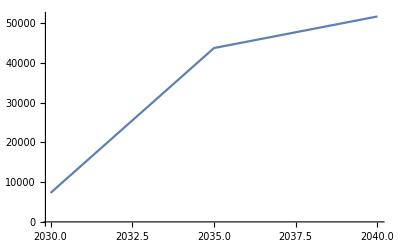

```mathematica
ListLinePlot[Transpose@{Range[2030,2040],prevAP[[2]][[13;;]]-prevDP[[2]][[13;;]]}]
```

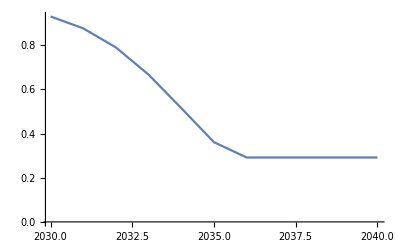

```mathematica
ListLinePlot[
Transpose@{Range[2030,2040],dataP[[4]][[4]][[2]][[400]][[31;;]]}]
```

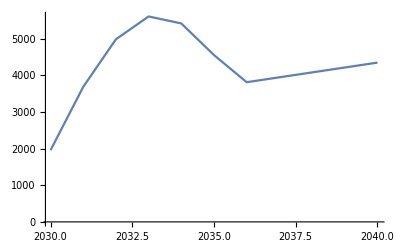

```mathematica
ListLinePlot[Transpose@{Range[2030,2040],dataP[[4]][[4]][[2]][[400]][[31;;]]*mAr[[1]][[2]][[400]]*(prevAP[[2]][[13;;]]-prevDP[[2]][[13;;]])}]
```

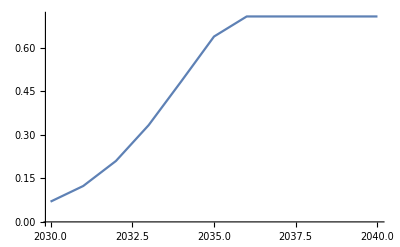

```mathematica
ListLinePlot[Transpose@{Range[2030,2040],(1-dataP[[4]][[4]][[2]][[400]][[31;;]])}]
```

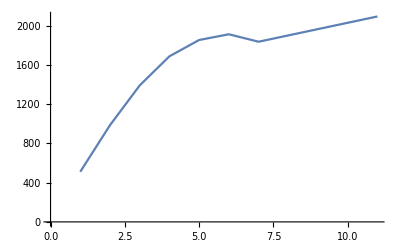

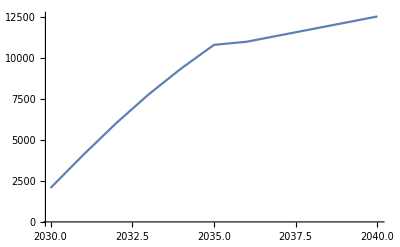

```mathematica
ListLinePlot[m3DP[[2]][[400]]]
ListLinePlot[Transpose@{Range[2030,2040],(dataP[[4]][[4]][[2]][[400]][[31;;]]*mAr[[1]][[2]][[400]]*(prevAP[[2]][[13;;]]-prevDP[[2]][[13;;]]))+((1-dataP[[4]][[4]][[2]][[400]][[31;;]])*mAs[[1]][[2]][[400]]*(prevAP[[2]][[13;;]]-prevDP[[2]][[13;;]]))}]
```

```mathematica
(*PNEUMONIA*)
d=1; (*indication #*)
m1DP=Table[prevDP[[i]][[;;12]]*dataP[[4]][[j]][[i]][[k]][[19;;30]]*mR[[d]][[i]][[k]]+prevDP[[i]][[;;12]]*(1-dataP[[4]][[j]][[i]][[k]][[19;;30]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2DP=Table[prevDP[[i]][[13;;]]*dataP[[4]][[j]][[i]][[k]][[31;;]]*mR[[d]][[i]][[k]]+prevDP[[i]][[13;;]]*(1-dataP[[4]][[j]][[i]][[k]][[31;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3DP=Table[(prevAP[[i]][[13;;]]-prevDP[[i]][[13;;]])*(dataP[[4]][[j]][[i]][[k]][[31;;]]*mAr[[d]][[i]][[k]]+(1-dataP[[4]][[j]][[i]][[k]][[31;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mDP=Table[Join[m1DP[[i]][[k]],m2DP[[i]][[k]]+m3DP[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdDP=Table[mDP[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtDP=Table[Total[Transpose[mdDP[[i]]]],{i,1,nop}]; (*total across years*)
mmDP=Table[Median[mdDP[[i]]],{i,1,nop}]; (*median (yearly)*)
```

```mathematica
(*BACTEREMIA*)
d=2; (*indication #*)
m1DB=Table[prevDB[[i]][[;;12]]*dataS[[4]][[j]][[i]][[k]][[19;;30]]*mR[[d]][[i]][[k]]+prevDB[[i]][[;;12]]*(1-dataS[[4]][[j]][[i]][[k]][[19;;30]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2DB=Table[prevDB[[i]][[13;;]]*dataS[[4]][[j]][[i]][[k]][[31;;]]*mR[[d]][[i]][[k]]+prevDB[[i]][[13;;]]*(1-dataS[[4]][[j]][[i]][[k]][[31;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3DB=Table[(prevAB[[i]][[13;;]]-prevDB[[i]][[13;;]])*(dataS[[4]][[j]][[i]][[k]][[31;;]]*mAr[[d]][[i]][[k]]+(1-dataS[[4]][[j]][[i]][[k]][[31;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mDB=Table[Join[m1DB[[i]][[k]],m2DB[[i]][[k]]+m3DB[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdDB=Table[mDB[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtDB=Table[Total[Transpose[mdDB[[i]]]],{i,1,nop}]; (*total across years*)
mmDB=Table[Median[mdDB[[i]]],{i,1,nop}]; (*median (yearly)*)
```

```mathematica
(*UTI*)
d=3; (*indication #*)
m1DU=Table[prevDU[[i]][[;;12]]*dataU[[4]][[j]][[i]][[k]][[19;;30]]*mR[[d]][[i]][[k]]+prevDU[[i]][[;;12]]*(1-dataU[[4]][[j]][[i]][[k]][[19;;30]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality from 2018 to intervention year*)

m2DU=Table[prevDU[[i]][[13;;]]*dataU[[4]][[j]][[i]][[k]][[31;;]]*mR[[d]][[i]][[k]]+prevDU[[i]][[13;;]]*(1-dataU[[4]][[j]][[i]][[k]][[31;;]])*mS[[d]][[i]][[k]],{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with carbapenems after intervention*)

m3DU=Table[(prevAU[[i]][[13;;]]-prevDU[[i]][[13;;]])*(dataU[[4]][[j]][[i]][[k]][[31;;]]*mAr[[d]][[i]][[k]]+(1-dataU[[4]][[j]][[i]][[k]][[31;;]])*mAs[[d]][[i]][[k]]),{i,1,nop},{k,1,ss*0.95}];
(*mortality associated with patients given alt therapy after intervention*)

mDU=Table[Join[m1DU[[i]][[k]],m2DU[[i]][[k]]+m3DU[[i]][[k]]],{i,1,nop},{k,1,ss*0.95}];

(*apply discounting*)
dr=0.03; (*discount rate*)
mdDU=Table[mDU[[i]][[k]][[t]]/((1+dr)^(t-1)),{i,1,nop},{k,1,ss*0.95},{t,1,Length[yearsI]}];
mtDU=Table[Total[Transpose[mdDU[[i]]]],{i,1,nop}]; (*total across years*)
mmDU=Table[Median[mdDU[[i]]],{i,1,nop}]; (*median (yearly)*)
```

#### plots etc.

```mathematica
Total[mdAB[[2]][[300]]]
Total[mdBB[[2]][[300]]]
Total[mdCB[[2]][[300]]]
Total[mdDB[[2]][[300]]]
```

26194.9

18923.6

21583.6

23974.1

```mathematica
Total[mmAB[[2]]]
Total[mmBB[[2]]]
Total[mmCB[[2]]]
Total[mmDB[[2]]]

Total[mmAB[[3]]]
Total[mmBB[[3]]]
Total[mmCB[[3]]]
Total[mmDB[[3]]]
```

26128.6

16863.3

19947.6

22869.7

66462.5

41662.4

48000.7

55066.9

```mathematica
Total[mmAP[[2]]]
Total[mmBP[[2]]]
Total[mmCP[[2]]]
Total[mmDP[[2]]]

Total[mmAP[[3]]]
Total[mmBP[[3]]]
Total[mmCP[[3]]]
Total[mmDP[[3]]]
```

202564.

174776.

187931.

198731.

306444.

272032.

273542.

282712.

```mathematica
Total[mmAU[[2]]]
Total[mmDU[[2]]]
Total[mmCU[[2]]]
Total[mmBU[[2]]]

Total[mmAU[[3]]]
Total[mmDU[[3]]]
Total[mmCU[[3]]]
Total[mmBU[[3]]]
```

329.754

467.69

527.336

573.303

6877.42

8374.59

8595.16

8543.24

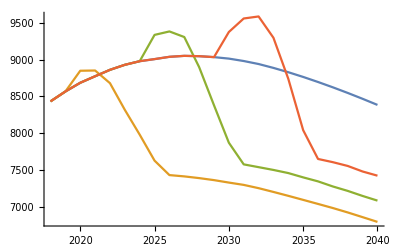

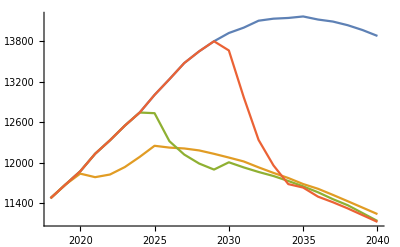

```mathematica
ListLinePlot[{Transpose@{Range[2018,2040],mmAP[[2]]},Transpose@{Range[2018,2040],mmBP[[2]]},Transpose@{Range[2018,2040],mmCP[[2]]},Transpose@{Range[2018,2040],mmDP[[2]]}}]
ListLinePlot[{Transpose@{Range[2018,2040],mmAP[[3]]},Transpose@{Range[2018,2040],mmBP[[3]]},Transpose@{Range[2018,2040],mmCP[[3]]},Transpose@{Range[2018,2040],mmDP[[3]]}}]
```

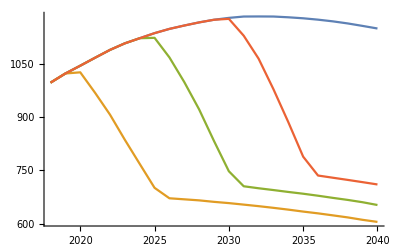

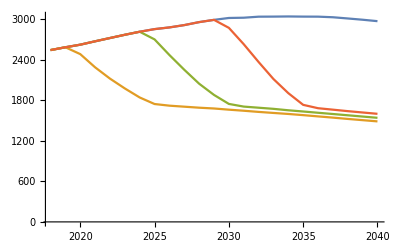

```mathematica
ListLinePlot[{Transpose@{Range[2018,2040],mmAB[[2]]},Transpose@{Range[2018,2040],mmBB[[2]]},Transpose@{Range[2018,2040],mmCB[[2]]},Transpose@{Range[2018,2040],mmDB[[2]]}}]

ListLinePlot[{Transpose@{Range[2018,2040],mmAB[[3]]},Transpose@{Range[2018,2040],mmBB[[3]]},Transpose@{Range[2018,2040],mmCB[[3]]},Transpose@{Range[2018,2040],mmDB[[3]]}}]
```

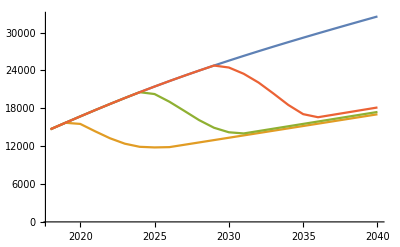

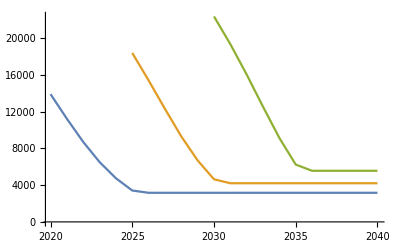

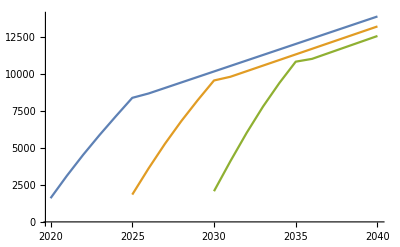

```mathematica
i=400;
ListLinePlot[{Transpose@{Range[2018,2040],mAP[[2]][[i]]},Transpose@{Range[2018,2040],mBP[[2]][[i]]},Transpose@{Range[2018,2040],mCP[[2]][[i]]},Transpose@{Range[2018,2040],mDP[[2]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m2BP[[2]][[i]]},Transpose@{Range[2025,2040],m2CP[[2]][[i]]},Transpose@{Range[2030,2040],m2DP[[2]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m3BP[[2]][[i]]},Transpose@{Range[2025,2040],m3CP[[2]][[i]]},Transpose@{Range[2030,2040],m3DP[[2]][[i]]}}]
```

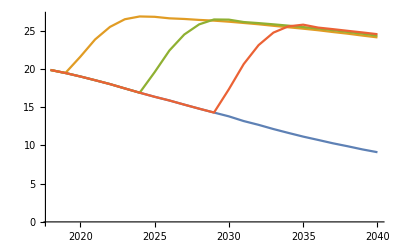

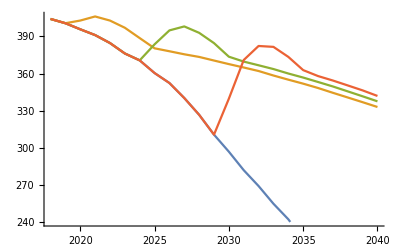

```mathematica
ListLinePlot[{Transpose@{Range[2018,2040],mmAU[[2]]},Transpose@{Range[2018,2040],mmBU[[2]]},Transpose@{Range[2018,2040],mmCU[[2]]},Transpose@{Range[2018,2040],mmDU[[2]]}}]
ListLinePlot[{Transpose@{Range[2018,2040],mmAU[[3]]},Transpose@{Range[2018,2040],mmBU[[3]]},Transpose@{Range[2018,2040],mmCU[[3]]},Transpose@{Range[2018,2040],mmDU[[3]]}}]
```

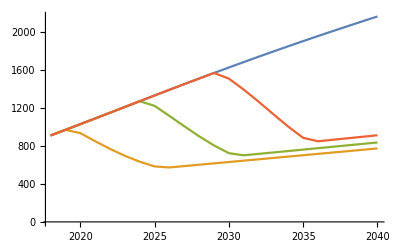

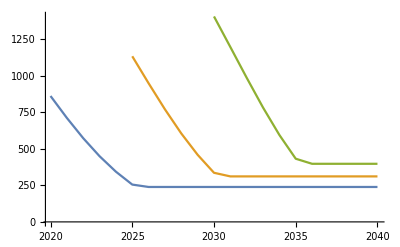

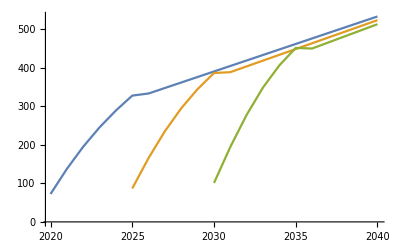

```mathematica
i=400;
ListLinePlot[{Transpose@{Range[2018,2040],mAB[[2]][[i]]},Transpose@{Range[2018,2040],mBB[[2]][[i]]},Transpose@{Range[2018,2040],mCB[[2]][[i]]},Transpose@{Range[2018,2040],mDB[[2]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m2BB[[2]][[i]]},Transpose@{Range[2025,2040],m2CB[[2]][[i]]},Transpose@{Range[2030,2040],m2DB[[2]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m3BB[[2]][[i]]},Transpose@{Range[2025,2040],m3CB[[2]][[i]]},Transpose@{Range[2030,2040],m3DB[[2]][[i]]}}]
```

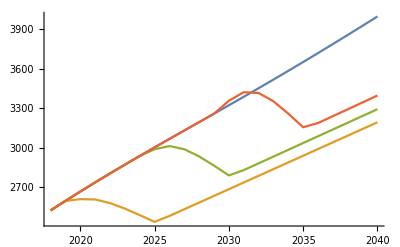

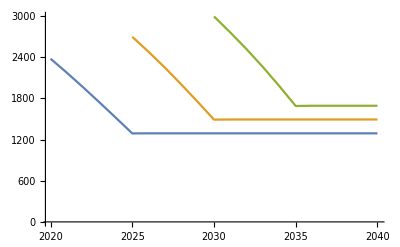

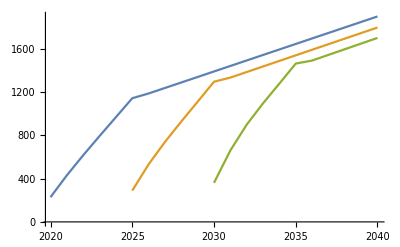

```mathematica
i=RandomInteger[{0,950},1][[1]];
ListLinePlot[{Transpose@{Range[2018,2040],mAB[[3]][[i]]},Transpose@{Range[2018,2040],mBB[[3]][[i]]},Transpose@{Range[2018,2040],mCB[[3]][[i]]},Transpose@{Range[2018,2040],mDB[[3]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m2BB[[3]][[i]]},Transpose@{Range[2025,2040],m2CB[[3]][[i]]},Transpose@{Range[2030,2040],m2DB[[3]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m3BB[[3]][[i]]},Transpose@{Range[2025,2040],m3CB[[3]][[i]]},Transpose@{Range[2030,2040],m3DB[[3]][[i]]}}]
```

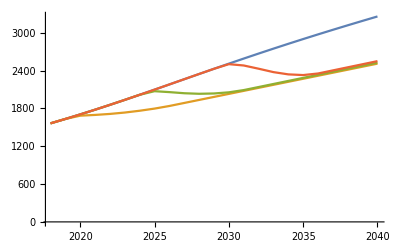

```mathematica
i=RandomInteger[{0,950},1][[1]];
ListLinePlot[{Transpose@{Range[2018,2040],mAB[[3]][[i]]},Transpose@{Range[2018,2040],mBB[[3]][[i]]},Transpose@{Range[2018,2040],mCB[[3]][[i]]},Transpose@{Range[2018,2040],mDB[[3]][[i]]}}]
```

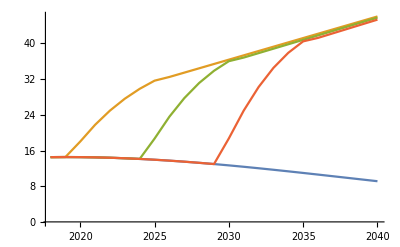

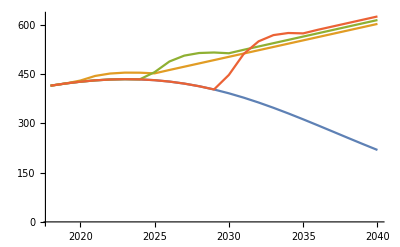

```mathematica
i=RandomInteger[{0,950},1][[1]];
ListLinePlot[{Transpose@{Range[2018,2040],mAU[[2]][[i]]},Transpose@{Range[2018,2040],mBU[[2]][[i]]},Transpose@{Range[2018,2040],mCU[[2]][[i]]},Transpose@{Range[2018,2040],mDU[[2]][[i]]}}]
ListLinePlot[{Transpose@{Range[2018,2040],mAU[[3]][[i]]},Transpose@{Range[2018,2040],mBU[[3]][[i]]},Transpose@{Range[2018,2040],mCU[[3]][[i]]},Transpose@{Range[2018,2040],mDU[[3]][[i]]}}]
```

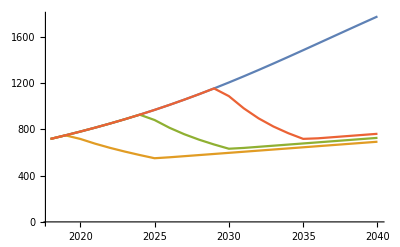

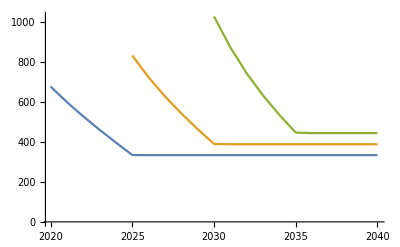

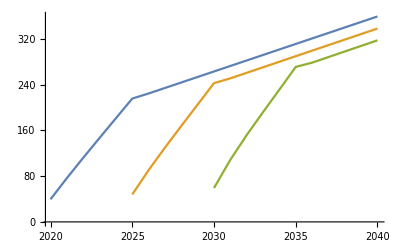

```mathematica
i=RandomInteger[{0,950},1][[1]];
ListLinePlot[{Transpose@{Range[2018,2040],mAU[[3]][[i]]},Transpose@{Range[2018,2040],mBU[[3]][[i]]},Transpose@{Range[2018,2040],mCU[[3]][[i]]},Transpose@{Range[2018,2040],mDU[[3]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m2BU[[3]][[i]]},Transpose@{Range[2025,2040],m2CU[[3]][[i]]},Transpose@{Range[2030,2040],m2DU[[3]][[i]]}}]
ListLinePlot[{Transpose@{Range[2020,2040],m3BU[[3]][[i]]},Transpose@{Range[2025,2040],m3CU[[3]][[i]]},Transpose@{Range[2030,2040],m3DU[[3]][[i]]}}]
```

```mathematica
mR[[3]][[2]][[i]]
mS[[3]][[2]][[i]]
mAr[[3]][[2]][[i]]
mAs[[3]][[2]][[i]]
```

0.00100113

0.0332222

0.0768687

0.030195

```mathematica
mR[[3]][[3]][[i]]
mS[[3]][[3]][[i]]
mAr[[3]][[3]][[i]]
mAs[[3]][[3]][[i]]
```

0.111798

0.063735

0.0585409

0.0278578

```mathematica
Median[mR[[3]][[2]]]
Median[mS[[3]][[2]]]
Median[mAr[[3]][[2]]]
Median[mAs[[3]][[2]]]
```

0.00819979

0.0387889

0.06869

0.0324374

```mathematica
Median[mR[[3]][[3]]]
Median[mS[[3]][[3]]]
Median[mAr[[3]][[3]]]
Median[mAs[[3]][[3]]]
```

0.00486026

0.0414049

0.0706781

0.0324718

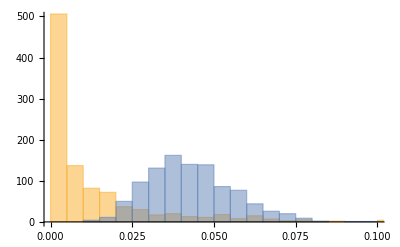

```mathematica
Histogram[{mR[[3]][[3]],mS[[3]][[3]]},PlotRange->{{0,0.1},{0,500}}]
```